# Pole friendly P_1 solver

## P_1 ODE Quadratic Solver

The IVP is
	y'' | = | f(z,y) | = | 6 y^2+z  with y(0)=y_0 and y'(0)=v_0
We can compute 
	y''(0)=6(y(0))^2+0=6 y_0^2
and approximate 
	y(h)≈y_0+h v_0+0.5 h^2 y''(0)=y_0+h v_0+0.5 h^2 y_0^2. 
Converting this to a fixed step size ODE solver is not too bad.  The first step is 
	y_1 | = | y_0+h v_0+0.5 h^2 y''(z_0)  | = | y_0+h v_0+0.5 h^2 f(z_0,y_0) 
v_1 | = | v_0+h v'(z_0)                             | = | v_0+h f(z_0,y_0)                           
The iteration (with a fixed step size h) is

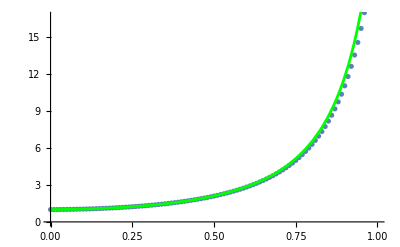

```mathematica
Clear[TwoStep]
TwoStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d},
y2d=6 yIn^2+zIn;
 {zIn + h, yIn+h vIn + 0.5 h^2 y2d, vIn + h y2d}
]
{h,n}={0.01,100};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
TwoData=NestList[TwoStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[TwoData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green]
]
```

There are two obvious problems with this:  the step is not accurate enough; the algorithm has no mechanism to adjust h.  There is a more subtle problem: the real solution does not look at all like a polynomial.

## P_1 ODE Taylor Series Solver

The ODE is
	y''=6 y^2+z  with y(0)=y_0 and y'(0)=v_0
we can differentiate to get
	y''' | = | 12y y'+1
y'''' | = | 12(y y''+(y')^2)
y''''' | = | 12 (y y'''+3y' y'')
… |   |  
We can  compute as many derivatives as we want and construct the Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
this will presumably be more accurate than the quadratic approximation.

```mathematica
Clear[FiveStep]
FiveStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

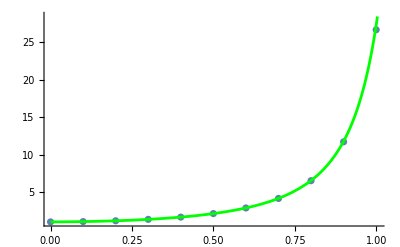

```mathematica
{h,n}={0.1,10};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
FiveData=NestList[FiveStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[FiveData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

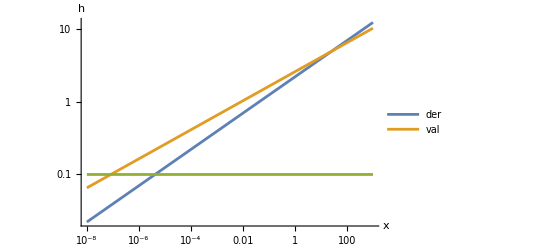

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d,h,γ=0.9},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[0.1,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

Now it is doing a good job of tracking the curve with small steps where needed.

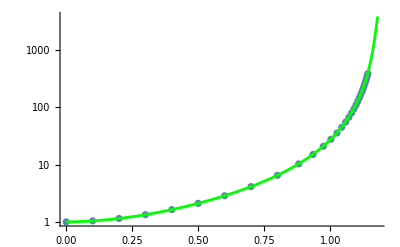

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-14;
FiveData=NestList[FiveStepTol[Tol],{0,y0,v0},30];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧]],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Target Interval and Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

-Graphics-

Our step size control Stepper for P_1 is

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d,h,γ=0.9},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[0.1,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

All we need to do to make it useful is to run it up to a target maximum interval.

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.